```mathematica
Clear["Globals`*"]
```

```mathematica
level[t_]:=.0002449t^2-0.478t+100.1
```

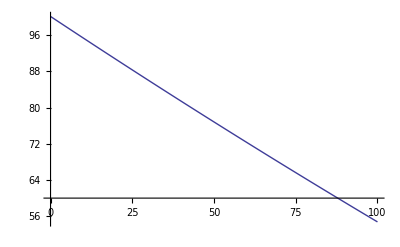

```mathematica
Plot[level[t], {t,0,100}]
```

```mathematica
Reduce[y==level[t] ,t]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

t==5.10614×10^-11 (1.91124×10^13-2827.87 √(2.60749×10^19+1.95843×10^17 y))||t==5.10614×10^-11 (1.91124×10^13+2827.87 √(2.60749×10^19+1.95843×10^17 y))

```mathematica
ToRadicals[%]
```

t==5.10614×10^-11 (1.91124×10^13-2827.87 √(2.60749×10^19+1.95843×10^17 y))||t==5.10614×10^-11 (1.91124×10^13+2827.87 √(2.60749×10^19+1.95843×10^17 y))

```mathematica
inva[y_]:=5.106140419497046*^-11 (1.911244999*^13-2827.868632026601 √(2.6074907603491004*^19+1.9584263609*^17 y))
```

```mathematica
invb[y_]:=5.106140419497046*^-11 (1.911244999*^13+2827.868632026601 √(2.6074907603491004*^19+1.9584263609*^17 y))
```

```mathematica
level[100]
```

54.749

```mathematica
inva[54.748999999999995]
```

100.

```mathematica
invb[54.748999999999995]
```

1851.82

```mathematica
FullSimplify[inva[y]]
```

975.909-1.44395×10^-7 √(2.60749×10^19+1.95843×10^17 y)

```mathematica
CForm[inva[level]]
```

5.106140419497046e-11*(1.911244999e13 - 
     2827.868632026601*Sqrt(2.6074907603491004e19 + 
        1.9584263609e17*level))